{2.94562,-0.00140662,-0.000495599}

Inverse::luc: 病态矩阵 {{5.,9889.,-92881.4},{9889.,1.95599×10^7,-1.84152×10^8},{-92881.4,-1.84152×10^8,1.86501×10^9}} 构成的 Inverse 的结果可能包含明显的数值错误.

{2.94562,-0.00140662,-0.000495599}

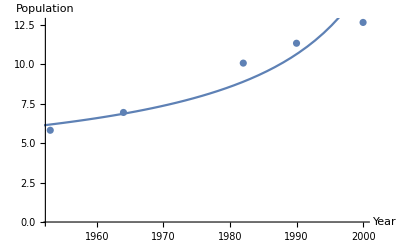

```mathematica
x={1953,1964,1982,1990,2000};
y={5.82,6.95,10.08,11.34,12.66};
ϕ0=ConstantArray[1,5];
ϕ1=x;
ϕ2=Table[-x[[i]]*y[[i]],{i,1,5}];
A=Transpose[{ϕ0,ϕ1,ϕ2}];
LeastSquares[A,y](*Inner function*)
(*My implementation below*)
ϕ[i_,x_]:=If[i==0,ϕ0[[x]],If[i==1,ϕ1[[x]],If[i==2,ϕ2[[x]]]]]
A=Table[Table[Sum[ϕ[i,k]*ϕ[j,k],{k,1,5}],{j,0,2}],{i,0,2}];
b=Table[Sum[ϕ[i,k]*y[[k]],{k,1,5}],{i,0,2}];
result=Inverse[A].b
Show[ListPlot[Table[{x[[i]],y[[i]]},{i,1,5}]],Plot[(result[[1]]+result[[2]]k)/(result[[3]]k+1),{k,1950,2010}],AxesLabel->{HoldForm[Year],HoldForm[Population]}]
```